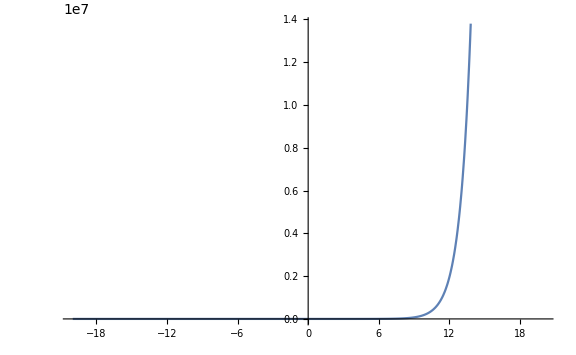

```mathematica
f[x_] := x*E^x+4
Plot[f[x],{x,-20,20},PlotRange->Automatic,ImageSize->Large]
```

(x (ⅇ^x+ⅇ^x x))/(4+ⅇ^x x)

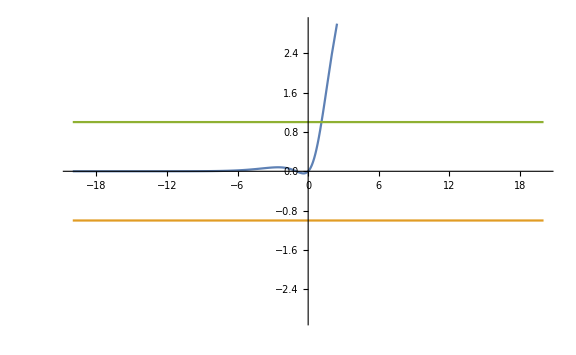

```mathematica
CONDREL[x_] := (x*f'[x])/f[x]
CONDREL[x]
Plot[{CONDREL[x],-1,1},{x,-20,20},PlotRange->{-3,3},ImageSize->Large]
```